# Funkcije:

### (* Ortogonalna baza *)

```mathematica
ortogonal[Β_,v_]:=Module[{Β1},Β1=Β;Βo=Table[Β1=ReplacePart[
Β1,i->Β1[[i]] - Sum[v[Β1[[i]],Β1[[k]]]/v[Β1[[k]],Β1[[k]]]* Β1[[k]],{k,1,i-1}]],{i,2,Length[Β]}][[Length[Β]-1]]]
(* V katero vstavimo bazo in skalarni produkt v obliki "v[v1_,v2_]:= Dot[v1,v2]" *)
```

```mathematica
(* Primer: *)
ClearAll[a,φ]
φ= {1,Sin[x],Cos[x]}
a[f_,g_] := Integrate[f g,{x,0,π}]
ortogonal[φ,a]
```

{1,Sin[x],Cos[x]}

{1,-2/π+Sin[x],Cos[x]}

### (* Ortonormirana baza; uporabimo funkcijo Orthogonalize[] v katero vstavimo bazo in skalarni produkt*)

```mathematica
(* Primer: *)
ClearAll[Χ]
Χ= {{1,2,0,0,3,3,1,1,1},{1,1,0,0,3,3,1,6,1},{1,2,7,0,3,0,0,1,1}};
Orthogonalize[Χ]
```

{{1/(√26),√(2/13),0,0,3/(√26),3/(√26),1/(√26),1/(√26),1/(√26)},{-3/(√17342),-16 √(2/8671),0,0,-9/(√17342),-9/(√17342),-3/(√17342),127/(√17342),-3/(√17342)},{260/(√24514251),550/(√24514251),7 √(667/36753),0,260 √(3/8171417),-407 √(3/8171417),-407/(√24514251),110/(√24514251),260/(√24514251)}}

### (* Projekcija na podprostor s produktom v, kjer naj bo Ψ ortogonalna ali ortonormirana baza, l pa vektor, ki ga projeciramo na Ψ *)

```mathematica
projUv[Ψ_,v_,l_]:=  Simplify[Sum[v[l,Ψ[[k]]]/v[Ψ[[k]],Ψ[[k]]]* Ψ[[k]],{k,1,Length[Ψ]}]]
```

```mathematica
(* Primer 1: *)(* Projeciramo x *)
ClearAll[a,φ,x]
a[f_,g_] := Integrate[f g,{x,0,π}]
φ={1,-2/π+Sin[x],Cos[x]};
projUv[φ,v,x]
```

v[x,1]/v[1,1]+(Cos[x] v[x,Cos[x]])/v[Cos[x],Cos[x]]+((-2/π+Sin[x]) v[x,-2/π+Sin[x]])/v[-2/π+Sin[x],-2/π+Sin[x]]

```mathematica
(* Primer 2: *)
ClearAll[a,φ,x]
a[f_,g_] := Integrate[f g,{x,0,π/2}]
φ=ortogonal[{1,Cos[x],Sin[x]},a]
projUv[φ,v,x]
```

{1,-2/π+Cos[x],-2/π-((1/2-2/π) (-2/π+Cos[x]))/(-2/π+π/4)+Sin[x]}

v[x,1]/v[1,1]+((-2/π+Cos[x]) v[x,-2/π+Cos[x]])/v[-2/π+Cos[x],-2/π+Cos[x]]+((4-2 π-2 (-4+π) Cos[x]+(-8+π^2) Sin[x]) v[x,(4-2 π-2 (-4+π) Cos[x]+(-8+π^2) Sin[x])/(-8+π^2)])/((-8+π^2) v[(4-2 π-2 (-4+π) Cos[x]+(-8+π^2) Sin[x])/(-8+π^2),(4-2 π-2 (-4+π) Cos[x]+(-8+π^2) Sin[x])/(-8+π^2)])

### (* Za lastne vrednosti uporabi Eigenvalues[], za lastne vektorje pa Eigenvectors[] *)

```mathematica
(* Primer: *)
Eigenvalues[{{1,-2,0},{0,3,-1},{1,1,1}}]
Eigenvectors[{{1,-2,0},{0,3,-1},{1,1,1}}]
```

{3,1+ⅈ,1-ⅈ}

{{-1,1,0},{-2+4 ⅈ,2+ⅈ,5},{-2-4 ⅈ,2-ⅈ,5}}

### (* Matrika linearne preslikave, kjer je ϕ baza in ψ predpis preslikave*)

```mathematica
matrikapreslikave[ϕ_,ψ_]:= (Transpose[Table[ψ[ϕ[[k]]],{k,1,Length[ϕ]}]].Inverse[Transpose[ϕ]])
```

```mathematica
(* Primer: *)
ClearAll[h,s1]
s1 = {{1,0,0},{0,1,0},{0,1,1}};
h[f_]:= Dot[f,a]* a + Cross[f, a]-2 f
matrikapreslikave[s1,h]//MatrixForm
(* poglejmo, še kaj je v jedru (NullSpace[]) *)
NullSpace[matrikapreslikave[s1,h]]
```

(-2+{1,0,0}×a+a {1,0,0}.a | {0,1,0}×a+a {0,1,0}.a | -{0,1,0}×a+{0,1,1}×a-a {0,1,0}.a+a {0,1,1}.a
{1,0,0}×a+a {1,0,0}.a | -2+{0,1,0}×a+a {0,1,0}.a | -{0,1,0}×a+{0,1,1}×a-a {0,1,0}.a+a {0,1,1}.a
{1,0,0}×a+a {1,0,0}.a | {0,1,0}×a+a {0,1,0}.a | -2-{0,1,0}×a+{0,1,1}×a-a {0,1,0}.a+a {0,1,1}.a)

{}

# Primeri:

#### Projekcija:

{1,-2/π+Cos[x],-π/4+x-((-4+π) (-2/π+Cos[x]))/(4 (-2/π+π/4))}

(8 (π^4+6 π^2 (-5+x)-192 (1+x)+72 π (2+x)-π^3 (2+3 x))+2 π (192-96 π+8 π^2+π^3) Cos[x])/(π (-384+192 π-32 π^2+π^4))

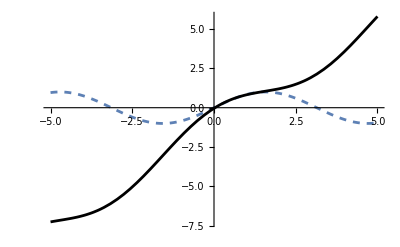

```mathematica
ClearAll[a,φ,x,b]
(* bazo podprostora φ ortagonaliziramo glede na skalarni produkt a in poiščemo projekcijo Sin[x] na podprostor, nato jo narišemo *)
φ= {1,Cos[x],x};
a[f_,g_] := Integrate[f g,{x,0,π/2}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,Sin[x]]
Plot[{Sin[x],b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

#### Rotacija za kot π/2 okoli premice x=z,y=0:

```mathematica
(* Razberemo smerni vektor s={1,0,1} poiščemo še dva pravokotna vektorja in ju ortonormirajmo 
v1={1/(√2),0,-1/(√2)} in v2={-1/(√2),0,1/(√2)}. Imamo ortonormirano bazo... ker predpis za preslikavo ni podan jo izračunamo sami. *)
ClearAll[A,v1,v2,v3]
A={{1/2,-1/(√2),1/2},{1/(√2),0,-1/(√2)},{1/2,1/(√2),1/2}};
A//MatrixForm
v1= {1/(√2),0,-1/(√2)};
v3={3,2,0};
v2={2,3,1};
Show[ParametricPlot3D[{t,0,t},{t,-10,10}],
Graphics3D[{Red,Line[{{0,0,0},v1}],Line[{{0,0,0},A.v1}],Green,Line[{{0,0,0},v2}],Line[{{0,0,0},A.v2}],Purple,Line[{{0,0,0},v3}],Line[{{0,0,0},A.v3}]}],
BoxRatios->{1, 1, 1},PlotRange->{{-3,3},{-3,3},{-3,3}}]
```

(1/2 | -1/(√2) | 1/2
1/(√2) | 0 | -1/(√2)
1/2 | 1/(√2) | 1/2)

-Graphics3D-

#### Projekcija:

{1,Cos[x],-2/π+Sin[x]}

1/3 (π^2-12 Cos[x]+(2 (-12+π^2) (-2+π Sin[x]))/(-8+π^2))

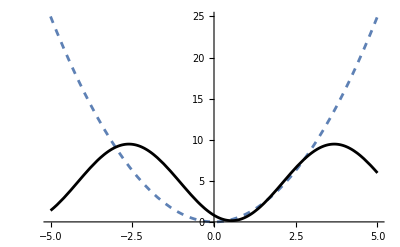

```mathematica
ClearAll[a,φ,x,b]
(* bazo podprostora φ ortagonaliziramo glede na skalarni produkt a in poiščemo projekcijo Sin[x] na podprostor, nato jo narišemo *)
φ= {1,Cos[x],Sin[x]};
a[f_,g_] := Integrate[f g,{x,0,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x^2]
Plot[{x^2,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

#### Projekcija:

{1,-π/2+x,-π^2/3+x^2-π (-π/2+x)}

(12 (π^4+60 π x-5 π^3 x-60 x^2+5 π^2 (-2+x^2)))/π^5

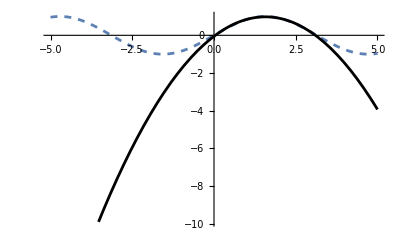

```mathematica
ClearAll[a,φ,x,b]
(* bazo podprostora φ ortagonaliziramo glede na skalarni produkt a in poiščemo projekcijo Sin[x] na podprostor, nato jo narišemo *)
φ= {1,x,x^2};
a[f_,g_] := Integrate[f g,{x,0,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,Sin[x]]
Plot[{Sin[x],b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,-1/2+x,-2/3 (-1/2+x) (1+Sin[1]/2)-Sin[1]/2+Sin[x]}

(-1+x-x Cos[1]+Sin[1]+(-1+Cos[1]) Sin[x])/(-1+Sin[1])

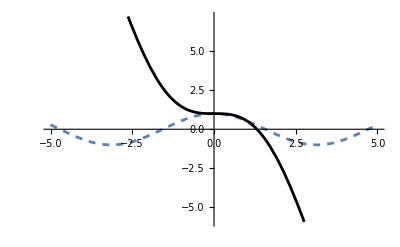

```mathematica
ClearAll[a,φ,x,b]
(* bazo podprostora φ ortagonaliziramo glede na skalarni produkt a in poiščemo projekcijo Sin[x] na podprostor, nato jo narišemo *)
φ= {1,x,Sin[x]};
a[f_,g_] := (f/.x->0)*(g/.x->0)+(f/.x->1) *(g/.x->1) +(D[f,x]/.x->0) *( D[g,x]/.x->0)  
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,Cos[x]]
Plot[{Cos[x],b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

# Aproksimacija:

#### Iskanje najboljše aproksimacije za f v podprostoru (zdi se kot, da je aproksimacija najboljša v sredini intervala na katerem integriramo)

{1,x,-π^2/3+x^2}

(3 x)/π^2

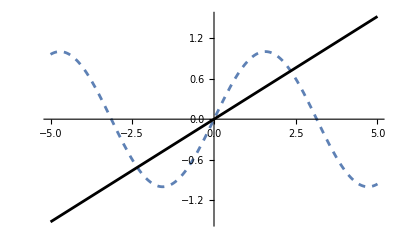

```mathematica
ClearAll[a,φ,x,b]
φ= {1,x,x^2};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,Sin[x]]
Plot[{Sin[x],b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,Cos[x],Sin[x]}

π^2/3-4 Cos[x]

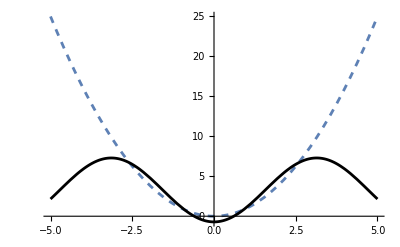

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x]};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x^2]
Plot[{x^2,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,Cos[x],Sin[x],x-2 Sin[x]}

(3 (60-10 π^2+π^4) (x-2 Sin[x]))/(5 (-6+π^2))+2 (-6+π^2) Sin[x]

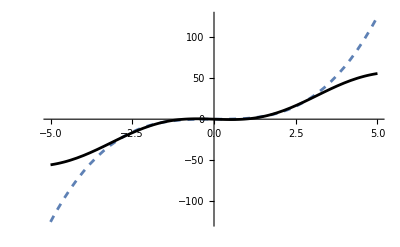

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x],x};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x^3]
Plot[{x^3,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,Cos[x],Sin[x],x-2 Sin[x],-π^2/3+x^2+4 Cos[x]}

1/2 ((-ⅇ^-π+ⅇ^π)/π+(6 (x-2 Sin[x]) (π Cosh[π]-2 Sinh[π]))/(π (-6+π^2))-(2 Cos[x] Sinh[π])/π+(2 Sin[x] Sinh[π])/π-(5 (π^2-3 x^2-12 Cos[x]) (-3 Cosh[π]+π Sinh[π]))/(-90+π^4))

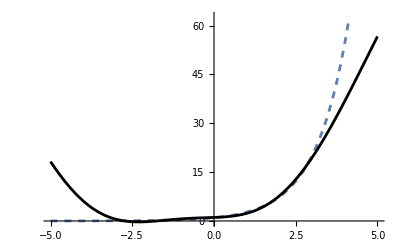

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x],x,x^2};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,E^x]
Plot[{E^x,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,Cos[x],Sin[x],-π+x+2 Sin[x],-(4 π^2)/3+x^2-4 Cos[x]+4 π Sin[x]-2 π (-π+x+2 Sin[x])}

1/4 ((2 (-1+ⅇ^(2 π)))/π+(5 (-3+ⅇ^(2 π) (-3+π)-π) (2 π^2-6 π x+3 x^2-12 Cos[x]))/(-90+π^4)+(6 (2+ⅇ^(2 π) (-2+π)+π) (-π+x+2 Sin[x]))/(π (-6+π^2))+(4 ⅇ^π Cos[x] Sinh[π])/π-(4 ⅇ^π Sin[x] Sinh[π])/π)

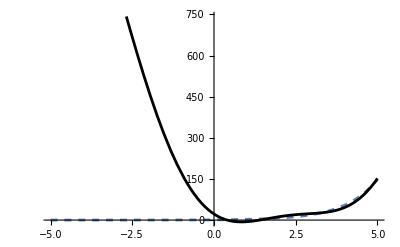

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x],x,x^2};
a[f_,g_] := Integrate[f g,{x,0,2π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,E^x]
Plot[{E^x,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,Cos[x],Sin[x],-3 π+x+2 Sin[x],-(28 π^2)/3+x^2-4 Cos[x]+12 π Sin[x]-6 π (-3 π+x+2 Sin[x])}

1/2 ⅇ^(2 π) ((3 (2+ⅇ^(2 π) (-2+π)+π) (-3 π+x+2 Sin[x]))/(π (-6+π^2))+(2 ⅇ^π Sinh[π])/π+(2 ⅇ^π Cos[x] Sinh[π])/π-(2 ⅇ^π Sin[x] Sinh[π])/π+(5 ⅇ^π (26 π^2-18 π x+3 x^2-12 Cos[x]) (-3 Cosh[π]+π Sinh[π]))/(-90+π^4))

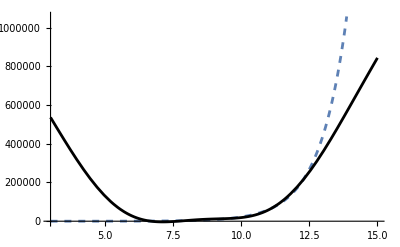

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x],x,x^2};
a[f_,g_] := Integrate[f g,{x,2π,4π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,E^x]
Plot[{E^x,b},{x,3,15},PlotStyle->{Dashed,Black}]
```

{1,Cos[x],x,-π^2/3+x^2+4 Cos[x],(3 ⅈ x)/4+1/2 (2-ⅈ π-2 Log[π])+Log[x]-(45 (-π^2/3+x^2+4 Cos[x]) ((4 π^3)/9-8 SinIntegral[π]))/(8 π (-90+π^4))+(2 Cos[x] SinIntegral[π])/π}

1/π(1/2800+ⅈ/2800) (560 π^(5/2)-1200 ⅈ π^(3/2) x-350 Cos[x] (3 √(2 π)+4 π^(5/2) (ExpIntegralE[-3/2,-ⅈ π]+ExpIntegralE[-3/2,ⅈ π]))+(175 (-π^2/3+x^2+4 Cos[x]) (8 π^(9/2)-45 (3 √(2 π)+4 π^(5/2) (ExpIntegralE[-3/2,-ⅈ π]+ExpIntegralE[-3/2,ⅈ π]))))/(-90+π^4)+(64 π^(5/2) (1-(ⅈ π)/2+(3 ⅈ x)/4-Log[π]+Log[x]+(5 (π^2-3 x^2-12 Cos[x]) (π^3-18 SinIntegral[π]))/(6 π (-90+π^4))+(2 Cos[x] SinIntegral[π])/π) (π^4 (56+45 π)+945 (-22+25 √2 FresnelC[√2])-225 π (18+7 (-2+3 √2 FresnelC[√2]) SinIntegral[π])))/(-12960+64 π^4-9 π^6+2880 π SinIntegral[π]+π^2 (810-288 SinIntegral[π]^2)))

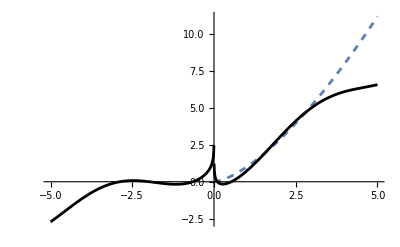

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],x,x^2,Log[x]};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,√(x^3)]
Plot[{√(x^3),Re[b]},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,1/2 (-1-Cos[1])+Cos[x],-Sin[1]/2-((1/2 (-1-Cos[1])+Cos[1]) (1/2 (-1-Cos[1])+Cos[x]) Sin[1])/((1+1/2 (-1-Cos[1]))^2+(1/2 (-1-Cos[1])+Cos[1])^2)+Sin[x]}

Tanh[x]

(Sin[1]+(-1+Cos[1]) Sin[x]-Tanh[1]+Cos[x] (-Sin[1]+Tanh[1]))/(-1+Cos[1])

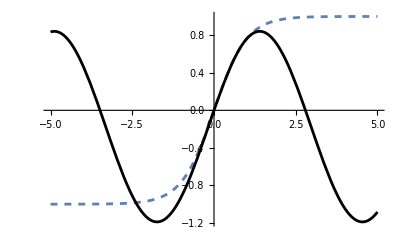

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x]};
a[f_,g_] := (f/.x->0)*(g/.x->0)+(f/.x->1) *(g/.x->1) +(D[f,x]/.x->0) *( D[g,x]/.x->0)  
ortogonal[φ,a]
t=Tanh[x]
b=projUv[ortogonal[φ,a],a,t]
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{1,1/2 (-1-Cos[1])+Cos[x],-Sin[1]/2-((1/2 (-1-Cos[1])+Cos[1]) (1/2 (-1-Cos[1])+Cos[x]) Sin[1])/((1+1/2 (-1-Cos[1]))^2+(1/2 (-1-Cos[1])+Cos[1])^2)+Sin[x]}

Cosh[x]

(Cos[1]+Cos[x] (-1+Cosh[1])-Cosh[1])/(-1+Cos[1])

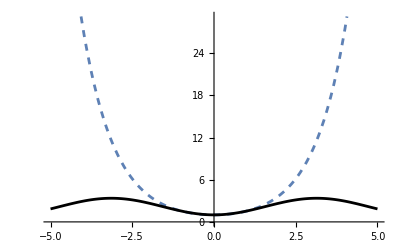

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x]};
a[f_,g_] := (f/.x->0)*(g/.x->0)+(f/.x->1) *(g/.x->1) +(D[f,x]/.x->0) *( D[g,x]/.x->0)  
ortogonal[φ,a]
t=Cosh[x]
b=projUv[ortogonal[φ,a],a,t]
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

9/4 Cos[9/4]+7/3 Cos[7/3]+5/2 Cos[5/2]+3 Cos[3]

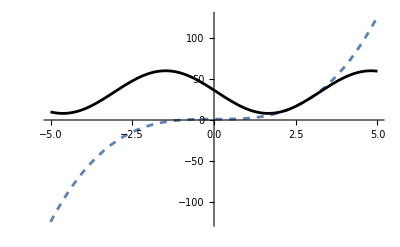

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x]};
tocke={1/4,1/3,1/2,1}+2
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
a[x,Cos[x]]
ortogonal[φ,a];
t=x^3+1;
b=projUv[ortogonal[φ,a],a,t];
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

9/4 Cos[9/4]+7/3 Cos[7/3]+5/2 Cos[5/2]+3 Cos[3]

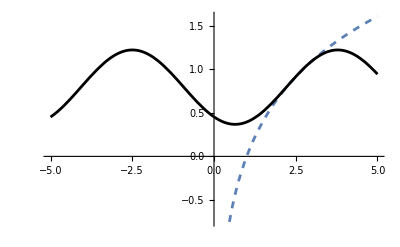

```mathematica
ClearAll[a,φ,x,b]
φ= {1,Cos[x],Sin[x]};
tocke={1/4,1/3,1/2,1}+2
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
a[x,Cos[x]]
ortogonal[φ,a];
t=Log[x];
b=projUv[ortogonal[φ,a],a,t];
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

9/4 Cos[9/4]+7/3 Cos[7/3]+5/2 Cos[5/2]+3 Cos[3]

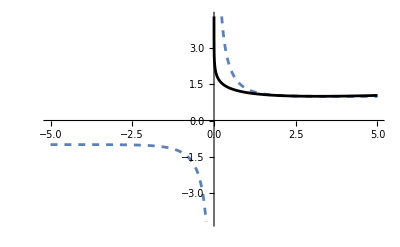

```mathematica
ClearAll[a,φ,x,b]
φ= {1,x,Log[x]};
tocke={1/4,1/3,1/2,1}+2
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
a[x,Cos[x]]
ortogonal[φ,a];
t=Coth[x];
b=projUv[ortogonal[φ,a],a,t];
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

9/4 Cos[9/4]+7/3 Cos[7/3]+5/2 Cos[5/2]+3 Cos[3]

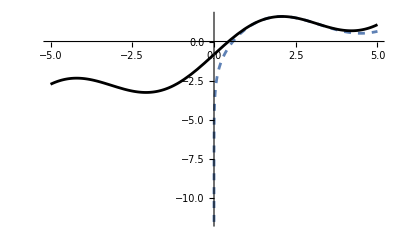

```mathematica
ClearAll[a,φ,x,b]
φ= {1,x,Sin[x]};
tocke={1/4,1/3,1/2,1}+2
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
a[x,Cos[x]]
ortogonal[φ,a];
t=Log[x]+ Sin[x];
b=projUv[ortogonal[φ,a],a,t];
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

9/4 Cos[9/4]+7/3 Cos[7/3]+5/2 Cos[5/2]+3 Cos[3]+13/4 Cos[13/4]+10/3 Cos[10/3]+7/2 Cos[7/2]+4 Cos[4]

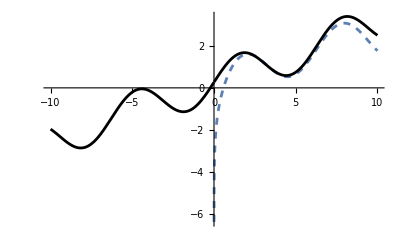

```mathematica
ClearAll[a,φ,x,b]
φ= {1,x,Sin[x]};
tocke={1/4,1/3,1/2,1,1+1/4,1+1/3,1+1/2,1+1}+2
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
a[x,Cos[x]]
ortogonal[φ,a];
t=Log[x]+ Sin[x];
b=projUv[ortogonal[φ,a],a,t];
Plot[{t,b},{x,-10,10},PlotStyle->{Dashed,Black}]
```

(x (-31500920230386+1560392751534 √2+1768885001680 √3+627071948627 √6+144 (-21802528956+1407660562 √2+1531964100 √3+603541245 √6) x^2)+(-19337293477204+2045008509475 √2+2033893867858 √3+480027105744 √6) Sin[π x])/(24 (-841993994403+48010326572 √2+53203058258 √3+20001129406 √6))

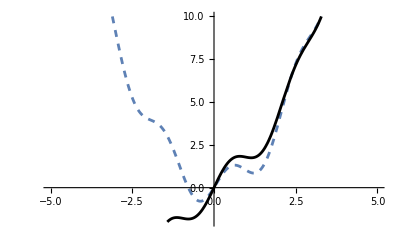

```mathematica
ClearAll[a,φ,x,b]
φ= {x,Sin[π x],x^3};
tocke={1/4,1/3,1/2,1,1+1/4,1+1/3,1+1/2,1+1}+2;
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
ortogonal[φ,a];
t=Sin[π x]+x^2;
b=projUv[ortogonal[φ,a],a,t]
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black},PlotRange->{-2,10}]
```

(2 Sin[π x] (126 Tan[4/3]-4 (16+9 √3) Tan[3/2]+9 (-4+3 √3) Tan[2])+x (288 Tan[4/3]-144 √3 Tan[3/2]+(-128+81 √3) Tan[2])+2 (-64+27 √3) Tan[x])/(6 (24 Tan[4/3]-12 √3 Tan[3/2]+(-16+9 √3) Tan[2]))

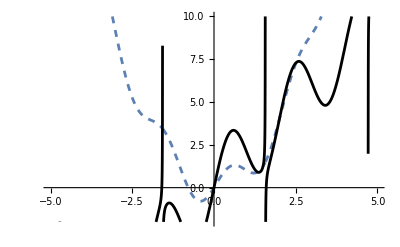

```mathematica
ClearAll[a,φ,x,b]
φ= {x,Sin[π x],Tan[x]};
tocke={1+1/3,1+1/2,1+1};
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
ortogonal[φ,a];
t=Sin[π x]+x^2;
b=projUv[ortogonal[φ,a],a,t]
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black},PlotRange->{-2,10}]
```

-32+(27 √3)/2+(-40+(63 √3)/4) x+(-11+(9 √3)/2) x^2

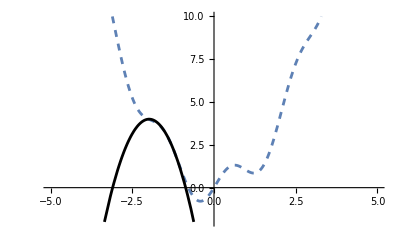

```mathematica
ClearAll[a,φ,x,b]
φ= {1,x,x^2};
tocke=-{1+1/3,1+1/2,1+1};
a[f_,g_] :=Sum[(f /.x->tocke[[i]])*(g /.x->tocke[[i]]),{i,1,Length[tocke]}]
ortogonal[φ,a];
t=Sin[π x]+x^2;
b=projUv[ortogonal[φ,a],a,t]
Plot[{t,b},{x,-5,5},PlotStyle->{Dashed,Black},PlotRange->{-2,10}]
```

#### Fourierjev razvoj

2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]

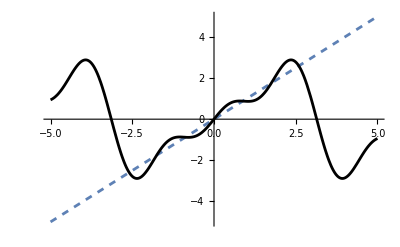

```mathematica
ClearAll[a,φ,x,b]
φ= {Sin[x],Cos[x],Sin[2 x],Cos[2 x],Sin[3 x],Cos[3 x]};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x]
Plot[{x,Re[b]},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{Sin[x],Cos[x],Sin[2 x],Cos[2 x],Sin[3 x],Cos[3 x]}

-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]

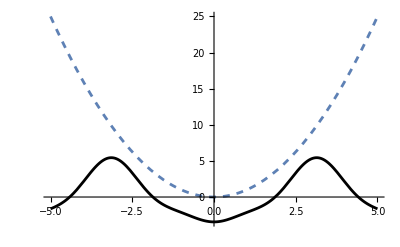

```mathematica
ClearAll[a,φ,x,b]
φ= {Sin[x],Cos[x],Sin[2 x],Cos[2 x],Sin[3 x],Cos[3 x]};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x^2]
Plot[{x^2,Re[b]},{x,-5,5},PlotStyle->{Dashed,Black}]
```

-Cos[x]+1/4 Cos[2 x]-1/9 Cos[3 x]+Sin[x]

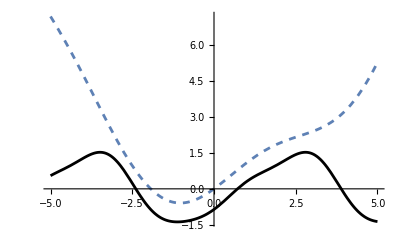

```mathematica
ClearAll[a,φ,x,b]
φ= {Sin[x],Cos[x],Sin[2 x],Cos[2 x],Sin[3 x],Cos[3 x]};
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,1/4 x^2+Sin[x]]
Plot[{1/4 x^2+Sin[x],Re[b]},{x,-5,5},PlotStyle->{Dashed,Black}]
```

-Cos[x]+1/4 Cos[2 x]-1/9 Cos[3 x]+1/16 Cos[4 x]-1/25 Cos[5 x]+1/36 Cos[6 x]-1/49 Cos[7 x]+1/64 Cos[8 x]-1/81 Cos[9 x]+1/100 Cos[10 x]+Sin[x]

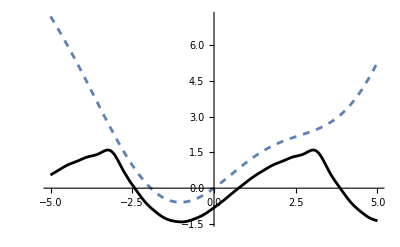

```mathematica
ClearAll[a,φ,x,b]
φ= Join[Table[Sin[i x],{i,1,10}],Table[Cos[i x],{i,1,10}]];
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,1/4 x^2+Sin[x]]
Plot[{1/4 x^2+Sin[x],Re[b]},{x,-5,5},PlotStyle->{Dashed,Black}]
```

-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x]+Sin[5 x]

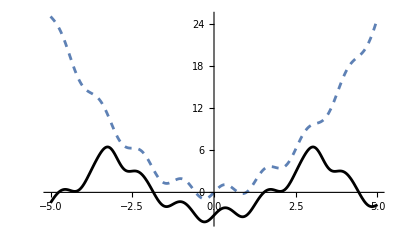

```mathematica
ClearAll[a,φ,x,b]
φ= Join[Table[Sin[i x],{i,1,10}],Table[Cos[i x],{i,1,10}]];
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x^2+Sin[5 x]]
Plot[{x^2+Sin[5 x],b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x],Cos[x],Cos[2 x],Cos[3 x],Cos[4 x],Cos[5 x],Cos[6 x],Cos[7 x],Cos[8 x],Cos[9 x],Cos[10 x]}

2 (120-20 π^2+π^4) Sin[x]-(15-10 π^2+2 π^4) Cos[x] Sin[x]+2/81 (40-60 π^2+27 π^4) Sin[3 x]-1/64 (15-40 π^2+32 π^4) Sin[4 x]+2/625 (24+25 π^2 (-4+5 π^2)) Sin[5 x]-1/162 (5-30 π^2+54 π^4) Sin[6 x]+(2 (120-980 π^2+2401 π^4) Sin[7 x])/16807-((15-160 π^2+512 π^4) Sin[8 x])/2048+(2 (40-540 π^2+2187 π^4) Sin[9 x])/19683-((3-50 π^2+250 π^4) Sin[10 x])/1250

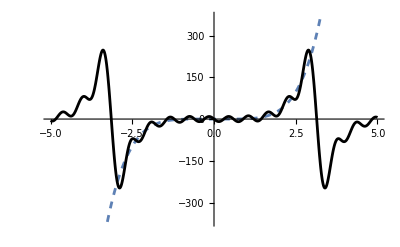

```mathematica
ClearAll[a,φ,x,b]
φ= Join[Table[Sin[i x],{i,1,10}],Table[Cos[i x],{i,1,10}]];
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a];
b=projUv[ortogonal[φ,a],a,x^5]
Plot[{x^5,b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x],Cos[x],Cos[2 x],Cos[3 x],Cos[4 x],Cos[5 x],Cos[6 x],Cos[7 x],Cos[8 x],Cos[9 x],Cos[10 x],1}

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x]+Sin[5 x]

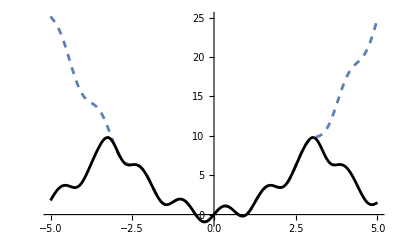

```mathematica
ClearAll[a,φ,x,b]
φ= Join[Table[Sin[i x],{i,1,10}],Table[Cos[i x],{i,1,10}],{1}];
a[f_,g_] := Integrate[f g,{x,-π,π}]
ortogonal[φ,a]
b=projUv[ortogonal[φ,a],a,x^2+Sin[5 x]]
Plot[{x^2+Sin[5 x],b},{x,-5,5},PlotStyle->{Dashed,Black}]
```

```mathematica
ClearAll[a,φ,x,b,t]
φ={Cos[x]Cos[y],Sin[x]Sin[y],Cos[2x]Cos[2y],Sin[2x]Sin[2y]};
a[f_,g_]:=Integrate[f g,{x,-π,π}]
t=1/5(x^2+y^2)+Cos[y]+x;
b=projekcija=projUv[φ,a,t]
Plot3D[{t,b},{x,-5,5},{y,-5,5},PlotStyle->{Red,Green},PlotPoints->15]
```

1/5 (-4 Cos[x]+Cos[2 x]+10 Sin[x]-5 Sin[2 x])

-Graphics3D-

```mathematica
ClearAll[a,φ,x,b,t]
φ={Cos[x]Cos[y],Sin[x]Sin[y],x,y};
a[f_,g_]:=Integrate[f g,{y,-π,π}]
t=1/5(x^2+y^2)+Cos[y]+x;
b=projekcija=projUv[φ,a,t]
Plot3D[{t,b},{x,-5,5},{y,-5,5},PlotStyle->{Red,Green},PlotPoints->15]
```

1/15 (π^2+3 x (5+x)+3 Cos[y])

-Graphics3D-

```mathematica
ClearAll[a,φ,x,b,t]
φ={x,x^2,y,y^2};
a[f_,g_]:=Integrate[f g,{x,-π,π},{y,-π,π}]
t=1/5(x^2+y^2)+Cos[y]+x;
b=projekcija=projUv[φ,a,t]
Plot3D[{t,b},{x,-5,5},{y,-5,5},PlotStyle->{Red,Green},PlotPoints->15]
```

x+(14 x^2)/45+2/45 (7-225/π^4) y^2

-Graphics3D-

```mathematica
ClearAll[a,φ,x,b,t]
φ={x,x^2,y,y^2};
a[f_,g_]:=Integrate[f g,{x,-π,π},{y,-π,π}]
t=Log[x+y^2]+Cos[2x];
b=projekcija=projUv[φ,a,t]
Plot3D[{t,Re[b]},{x,-5,5},{y,-5,5},PlotStyle->{Red,Green},PlotPoints->15]
```

1/(1260 π^6)(189 π^2 x (2 π^4+10 π^3 ArcCoth[π]-2 π^5 ArcCoth[π]+8 π^(5/2) (ArcTan[√π]-ArcTanh[√π]))+70 y^2 (18 π^5 ArcCoth[π]-12 π^(5/2) (ArcTan[√π]-ArcTanh[√π])+π^4 (-38+30 Log[π]+15 Log[-1+π^2]))+50 π^2 x^2 (63-6 π^4+6 π^5 ArcCoth[π]+36 π^(3/2) (ArcTan[√π]+ArcTanh[√π])+π^2 (-86+42 Log[π]+21 Log[-1+π^2])))

-Graphics3D-

```mathematica
Show[%247,ViewPoint->Left]
```

-Graphics3D-

```mathematica
Show[%247,ViewPoint->Front]
```

-Graphics3D-